```mathematica
Clear["`*"]
```

```mathematica
j=I;
```

```mathematica
(*Transfer Function*)
A=Abs[1/(√(1+(2 Pi f R c)^2))];

(*Parameters*)
lowPoleFrequency=5000;
lowPoleDBCuttoff= 1/(√2);

(*Solution*)
solve=Solve[A==lowPoleDBCuttoff,{f,R,c}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→-1/(2 f π R)},{c→1/(2 f π R)},{c→-(ⅈ √3)/(2 f π R)},{c→(ⅈ √3)/(2 f π R)}}

1/200 ⅇ^(-(ⅈ ω^2)/(20000 π)) (-ⅈ FresnelC[ω/(100 π)]-ⅈ FresnelC[100-ω/(100 π)]+FresnelS[ω/(100 π)]+FresnelS[100-ω/(100 π)]+ⅇ^((ⅈ ω^2)/(10000 π)) (-ⅈ FresnelC[ω/(100 π)]+ⅈ FresnelC[100+ω/(100 π)]-FresnelS[ω/(100 π)]+FresnelS[100+ω/(100 π)]))

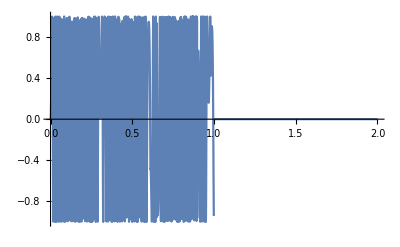

```mathematica
f0=0;
fmax=5000;
T=1;
k=(fmax-f0)/T;
V=Sin[2Pi(f0 t+k/2 t^2)](UnitStep[t]-UnitStep[t-T]);

Vω=FourierTransform[V,t,ω,FourierParameters->{1,-1}]

Plot[V,{t, 0, 2}]
```

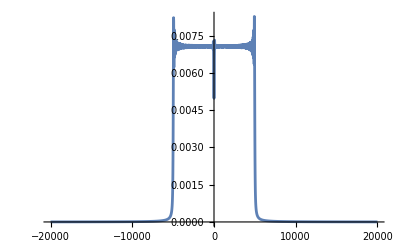

```mathematica
Plot[Abs[Vω]/.{ω-> 2 Pi f},{f, -20000, 20000}, PlotRange->All]
```